```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
```

```mathematica
sumIntDigits[17, 10]
```

8

```mathematica
sumIntDigits[10, 2]
```

2

```mathematica
expSumList[n_ ,b_, p_]:=Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]]
```

```mathematica
Range[4.23123]
```

{1,2,3,4}

```mathematica
expSumList[1000,10, 4];
```

```mathematica
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p]]
```

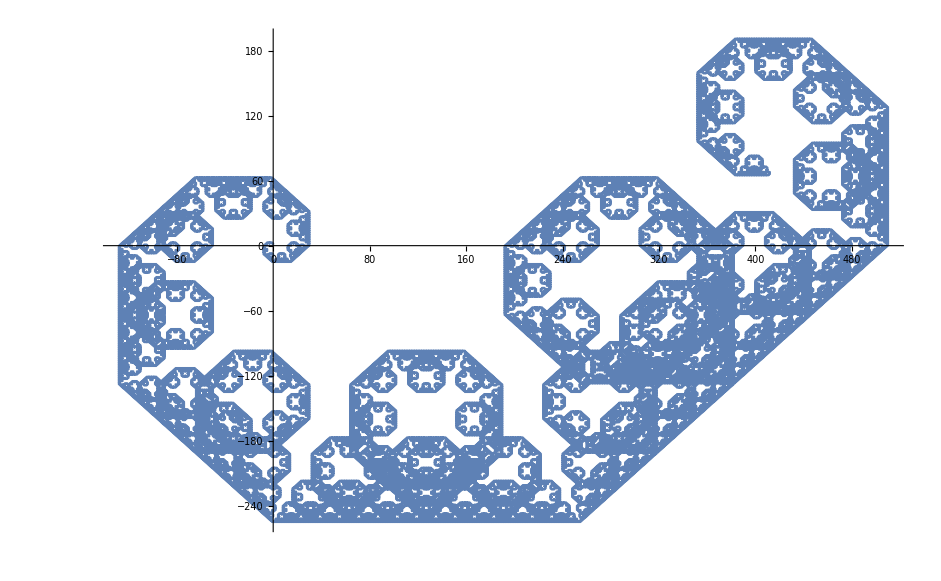

```mathematica
visualizer[100000, 2, 4]
```

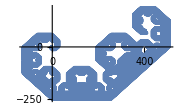

```mathematica
Show[%430,ImageSize->Small]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param p *)
```

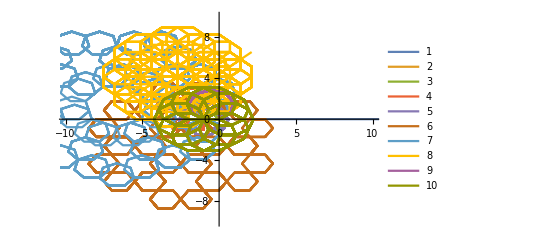

```mathematica
ListLinePlot[(ReIm /@ expSumList[1000, 10, #])& /@ Range[10],PlotRange->{{-10, 10},{-10, 10}}, PlotLegends->Range[10]]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param n *)
```

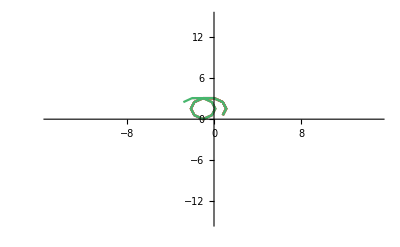

```mathematica
ListLinePlot[(ReIm /@ expSumList[#, 10, 10])& /@ Range[15],PlotRange->{{-15, 15},{-15, 15}}]
```

```mathematica
(* Table of some integer visualizations varying in base *)
```

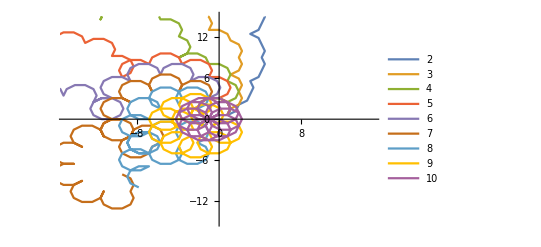

```mathematica
ListLinePlot[(ReIm /@ expSumList[100, #, 10])& /@ Range[2,10],PlotRange->{{-15, 15},{-15, 15}}, PlotLegends->Range[2,10]]
```

```mathematica
randomRealTable = RandomReal[25, 15]  (* 15 random real numbers ranging from 0 to 25 *)
```

{2.02558,8.2337,9.18125,12.7486,4.62029,1.85226,13.4382,9.99327,11.7245,13.3529,6.27674,5.16695,18.3634,17.7452,1.50481}

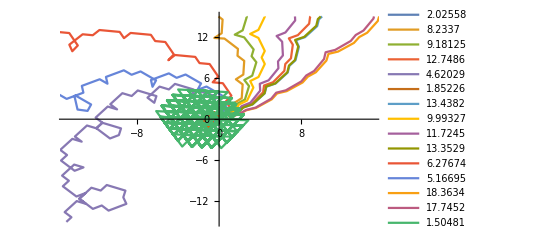

```mathematica
ListLinePlot[(ReIm /@ expSumList[1000, 2, #])& /@  randomRealTable,PlotRange->{{-15, 15},{-15, 15}}, PlotLegends->randomRealTable]
```

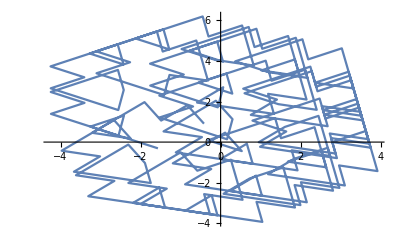

```mathematica
visualizer[250, 2, Pi]
```

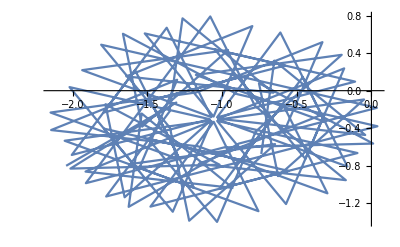

```mathematica
visualizer[100, 10, GoldenRatio]
```

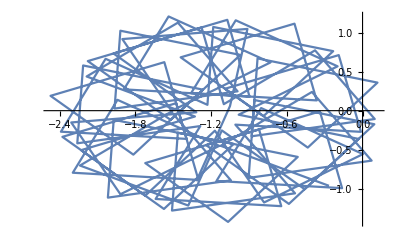

```mathematica
visualizer[100, 10, Sqrt[2]]
```